```mathematica
(* ФН2-72Б *)
(* Вариант 15 *)
(* Толщина сплошных линий *)
thick=0.005;
(* Толщина линий силовых факторов *)
thickF=0.003;
(* Размер стрелочек осей *)
arr=0.03;
(* Размер стрелочек силовых факторов *)
arrF=0.03;
(* Высота шарниров *)
d=0.5;
(* Оси координат *)
axes=Graphics[{Arrowheads[{0.0,arr}],Arrow[{{0,0},{3.5,0}}],Arrow[{{0,0},{0,0.85}}],Text[Style["x_1",18,FontFamily->Times],{3.4,-0.115}],Text[Style["x_2",18,FontFamily->Times],{-0.125,0.75}]}];
(* Точки O и B *)
points=Graphics[{Text[Style["O",16,FontFamily->Times],{-0.125,0.1}],Text[Style["B",16,FontFamily->Times],{3.125,0.1}]}];
(* Балка *)
balka=Graphics[{Thickness[thick],Line[{{0,0},{3,0}}],Text[Style["L",16,FontFamily->Times],{1.125,-0.1}],Text[Style["2L",16,FontFamily->Times],{2.125,-0.1}],Text[Style["3L",16,FontFamily->Times],{3.125,-0.1}]}];
(* Шарнир в точке Subscript[x, 1] = x *)
sharnir[x_]:=Graphics[{Thickness[thick],Line[{{x,0},{x,-d}}],Line[{{x-0.2,-d},{x+0.2,-d}}],EdgeForm[{Thickness[thick],Black}],White,Disk[{x,0},0.05],Disk[{x,-d},0.05]}];
(* Штриховка в точке Subscript[x, 1] = x с шагом h *)
dash[x_,h_]:=Graphics[{Thickness[0.003]}~Join~Table[Line[{{x-0.3+i*h,-d},{x-0.2+i*h,-d-0.1}}],{i,0,IntegerPart[0.5/h]}]~Join~{White}~Join~Table[Rectangle[{x+sign*0.2,-d+0.05},{x+sign*0.4,-d-0.125}],{sign,-1,1,2}]];
(* Шарнирная опора в точке Subscript[x, 1] = x *)
opora[x_]:=Graphics[{Thickness[thick],Line[{{x-0.2,-d},{x+0.2,-d}}],White,EdgeForm[{Thickness[thick],Black}],Triangle[{{x,0},{x-0.15,-d},{x+0.15,-d}}],EdgeForm[{Thickness[thick],Black}],White,Disk[{x,0},0.05]}];
(* Сила в точке Subscript[x, 1] = x знака sign *)
forse[x_,sign_,label_]:=Graphics[{Thickness[thickF],Lighter@Blue,Arrowheads[{0.0,arrF}],Arrow[{{x,0},{x,-sign*0.5}}],Text[Style[label,16,FontFamily->Times],{x+0.125,-sign*0.5}]},PlotRange->All];
(* Момент в точке Subscript[x, 1] = x знака sign *)
moment[x_,sign_,label_]:=Graphics[{Thickness[thickF],Darker@Green,Arrowheads[arrF],Arrow[{{x,0},{x+sign*0.15,-0.25},{x+sign*0.3,-0.1}}],Text[Style[label,16,FontFamily->Times],{x+sign*0.2,-0.35}]}];
(* Равномерная нагрузка на участке (a, b) знака sign с числом стрелочек n и подписью в координате k(a + b) *)
qr[a_,b_,sign_,n_,label_,k_]:=Graphics[{Thickness[thickF],Red,Line[{{a,sign*0.3},{b,sign*0.3}}],Text[Style[label,16,FontFamily->Times],{k*(a+b),sign*0.425}],Arrowheads[arrF]}~Join~Table[Arrow[{{a+(0.5+i)*(b-a)/n,sign*0.3},{a+(0.5+i)*(b-a)/n,0}}],{i,0,n-1}]];
```

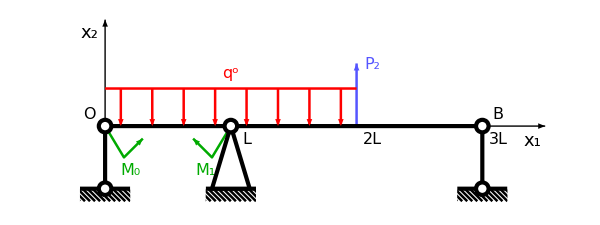

```mathematica
(* Схема нагружения в соответствии с вариантом *)
Print@Show[{axes,points,dash[0,0.04],dash[1,0.04],dash[3,0.04],moment[0,1,"M_0"],moment[1,-1,"M_1"],forse[2,-1,"P_2"],qr[0,2,1,8,"q^o",1/2],balka,sharnir[0],opora[1],sharnir[3]},ImageSize->600];
```

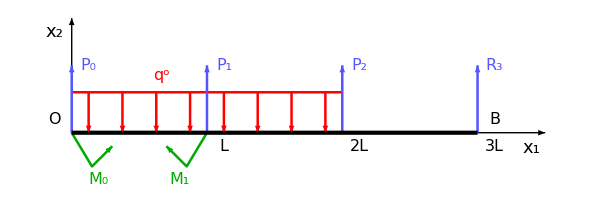

```mathematica
(* Переход к статически определимой балке *)
Print@Show[axes,points,qr[0,2,1,8,"q^o",1/3],forse[3,-1,"R_3"],forse[1,-1,"P_1"],moment[0,1,"M_0"],moment[1,-1,"M_1"],forse[2,-1,"P_2"],forse[0,-1,"P_0"],balka,ImageSize->600]
```

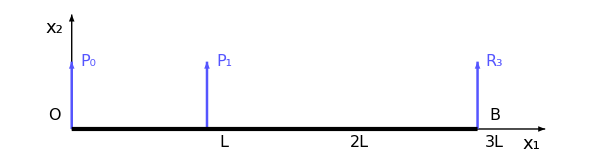

```mathematica
(* Балка под действием только реакции Subscript[R, 0] *)
Print@Show[axes,points,forse[0,-1,"P_0"],forse[1,-1,"P_1"],forse[3,-1,"R_3"],balka,ImageSize->600]
```

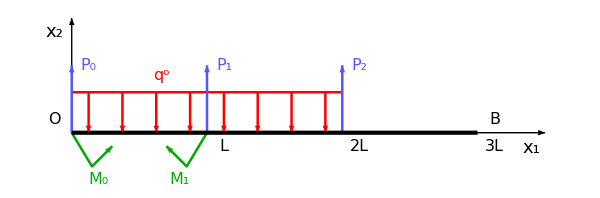

```mathematica
(* Переход к статически определимой балке *)
Print@Show[axes,points,qr[0,2,1,8,"q^o",1/3],forse[0,-1,"P_0"],forse[1,-1,"P_1"],moment[0,1,"M_0"],moment[1,-1,"M_1"],forse[2,-1,"P_2"],balka,ImageSize->600]
```